# Blatt 10

Jonas Neundorf & Jan Skottke

Phasenvorschub

Zunächst definieren wir die Linse und den Driftweg.

```mathematica
mF[f_] := {{1, 0}, {-1/f, 1}}(* dünne Linse *)
```

```mathematica
m0[L_] := {{1, L}, {0, 1}} (* Driftmatrix *)
```

Berechne nun die Gesamtmatrix der FODO-Struktur. Beachte dabei, dass wir uns in die Mitte der Linse setzten und somit 2f fuer den Anfang und das Ende einsetzten muessen.

```mathematica
fodo = mF[2*f].m0[L].mF[-f].m0[L].mF[2*f] //FullSimplify
```

{{1-L^2/(2 f^2),(L (2 f+L))/f},{(L (-2 f+L))/(4 f^3),1-L^2/(2 f^2)}}

Alternativ lässt sich die Entwicklung der Koordinaten auch mit den Twiss-Parametern beschreiben. Nach dem Durchqueren einer FODO-Zelle sollen sie die gleichen Werte wie vorher haben, damit vereinfacht sich die Matrix zu

```mathematica
mM:= {{Cos[ϕ]+α*Sin[ϕ],β*Sin[ϕ]},{-(1+α^2)/β*Sin[ϕ],Cos[ϕ]-α*Sin[ϕ]}}
```

Da beide Matritzen die gleiche Transformation beschreiben, müssen sie gleich sein. Damit ist auch ihre Spur gleich. Daraus lässt sich der Phasenvorschub berechnen.

```mathematica
ze =Solve[Tr[mM] ==Tr[fodo],Cos[ϕ]]//.Rule-> Equal//FullSimplify//Flatten
```

{L^2/(2 f^2)+Cos[ϕ]==1}

```mathematica
zek=ze//.L^2/f^2-> 1/κ^2
```

{1/(2 κ^2)+Cos[ϕ]==1}

```mathematica
kap=Solve[zek,κ][[2]]
```

{κ→1/(√2 √(1-Cos[ϕ]))}

```mathematica
zer=Solve[Tr[mM] ==Tr[fodo],Cos[ϕ]]//FullSimplify//Flatten
```

{Cos[ϕ]→1-L^2/(2 f^2)}

```mathematica
zer= zer //.L^2/f^2-> 1/κ^2
```

{Cos[ϕ]→1-1/(2 κ^2)}

```mathematica
p = Solve[ze,ϕ][[2]]//FullSimplify//Flatten
```

{ϕ→ConditionalExpression[ArcCos[1-L^2/(2 f^2)]+2 π C[1],C[1]∈Integers]}

{ϕ→ConditionalExpression[ArcCos[1-L^2/(2 f^2)]+2 π C[1],C[1]∈Integers]}

Der Phasenvorschub ist somit

```mathematica
phase= ϕ-> ArcCos[1-L^2/(2*f^2)] //.L^2/f^2-> 1/κ^2
```

ϕ→ArcCos[1-1/(2 κ^2)]

Berechnen wir nun β:

```mathematica
eq=Sin[ϕ]== √(1-Cos[ϕ]^2);
```

```mathematica
sinus=Solve[eq//.zer,Sin[ϕ]]//FullSimplify//Flatten//.L/f-> 1/κ
```

{Sin[ϕ]→1/2 √((-1+4 κ^2)/κ^4)}

```mathematica
MatrixForm[mM ]== MatrixForm[fodo]
```

(Cos[ϕ]+α Sin[ϕ] | β Sin[ϕ]
-((1+α^2) Sin[ϕ])/β | Cos[ϕ]-α Sin[ϕ])==(1-L^2/(2 f^2) | (L (2 f+L))/f
(L (-2 f+L))/(4 f^3) | 1-L^2/(2 f^2))

```mathematica
βPhasef = Solve[mM[[1,2]]==fodo[[1,2]]//.sinus,β]//FullSimplify//Flatten
```

{β→(2 L (2 f+L))/(f √((-1+4 κ^2)/κ^4))}

```mathematica
beta= β-> (4*L)/(√((-1+4 κ^2)/κ^4))+(2*L)/(κ*√((-1+4*κ^2)/κ^4))//FullSimplify
```

β→(2 L (1+2 κ))/(κ √((-1+4 κ^2)/κ^4))

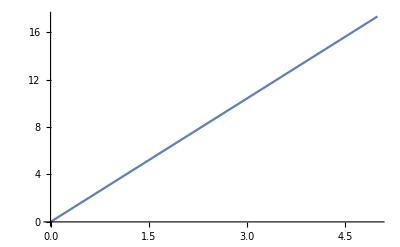

```mathematica
Plot[β//.beta//.κ-> 1,{L,0,5}]
```

```mathematica
fo = m0[L].mF[f]
```

{{1-L/f,L},{-1/f,1}}

```mathematica
βPhased= Solve[mM[[1,2]]==fo[[1,2]]//.sinus,β]//FullSimplify//Flatten
```

{β→(2 L)/(√((-1+4 κ^2)/κ^4))}

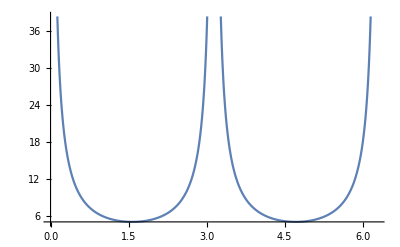

```mathematica
Plot[β//.βPhased//.kap//.L-> 5,{ϕ,0,2*Pi}]
```

```mathematica
β[s_] = (2 Abs[s-L] (1+2 κ))/(κ √((-1+4 κ^2)/κ^4))
```

(2 (1+2 κ) Abs[-L+s])/(κ √((-1+4 κ^2)/κ^4))